# Fidelities of quantum channels

What is the fidelity between a (possibly lossy) quantum channel E(ρ) and a unitary channel U(ρ) = u.ρ.u†? We can calculate it using the methods presented in:

Michael A. Nielsen, A simple formula for the average gate fidelity of a quantum dynamical operation, 
Journal reference:	Phys. Lett. A 303 (4): 249-252 (2002)
DOI:	10.1016/S0375-9601(02)01272-0
(In particular, we use Eq. 3, where the entanglement entropy is given in Eq. 16.)

Alternatively, one can write a channel on a d-dimensional hilbert space as a d^2 dimensional operator that acts on a (flattened) d*d dimensional density matrix. This is called the Liouville representation of the channel. More info can be found in Jonas Helsen’s thesis, section 2.3.1. (https://pure.tudelft.nl/portal/files/53781796/dissertation.pdf)

The most important functionality is GateFidelityProcessVsUnitary[process_,unitary_]. Process needs to be any function with a single argument, that sends a d-dimensional density matrix to another density matrix (we don’t care how it’s implemented). Unitary needs to be a d*d unitary matrix.

```mathematica
(* Make a matrix element of the form | a > < b | *)
KetBra[ ket_, bra_ ] := Outer[Times, ket, Conjugate[bra] ];   

(* Create a basis for dim-dimensional unitary matrices. We choose the ones proposed in Nielsen (2002), but any basis would do.   *)
generalX[dim_]:=  IdentityMatrix[dim, SparseArray ][[ RotateRight[ Range[dim] ] ]]  ;
generalZ[dim_]:= DiagonalMatrix[ SparseArray[ Table[ Exp[ 2 Pi I j / dim ], {j,0,dim-1} ] ]];
unitaryBasis[dim_] := Module[{xx, zz, basis},
xx = generalX[ dim ];
zz  = generalZ[dim];
basis = Table[ MatrixPower[ xx, k ] . MatrixPower[ zz, l ], {k,0,dim-1}, {l,0,dim-1} ];
Return[ (1/Sqrt@dim) * Flatten[ basis, 1 ] ];
];

(* Represent a quantum process (i.e. channel) in its Liouville matrix form. Then, Flatten[ process[ rho ] ] == channel.Flatten[rho].  *)
(* Variable "process" must be any mapping from N-dimensional density matrix to another N-dimensional density matrix.  *)
LiouvilleRepresentation[ process_ , dim_ ] := Module[{basis, channel},
basis = unitaryBasis[dim];
channel =  SparseArray@Sum[ 
KetBra[     Flatten@process[ p ]    ,   Flatten[p]     ]    
,{p, basis} ];
Return[channel];
];


(* Variable "process" must be any mapping from N-dimensional density matrix to another N-dimensional density matrix.  *)
GateFidelityFromProcess[ process_, dim_  ]:= Module[{basis, entanglementFid },
basis = unitaryBasis[dim];
entanglementFid =  Sum[   Tr[  p† . process[p] ], {p, basis}] / dim^2 ;
(* This is the Entanglement Fidelity defined in Nielsen (2002), properly normalized so one can check the values. We're differ a factor of dim from Nielsen because we do normalize our basis. *) 
Return[ (dim^3 * entanglementFid +dim^2) / (dim^2 (dim+1 )  ) ];
];

(* Find the closeness of a channel to the identity operation. *)
GateFidelityFromChannel[ channel_ ]:= Module[{dim},
dim = Sqrt@ Length[channel] ;
Return[  1/(dim+1) * (1/dim * Tr[ channel ] + 1 ) ];
]

GateFidelityProcessVsUnitary[ process_, unitary_ ] := Module[{dim, concatProcess},
dim = Length@unitary;
concatProcess[rho_]:= unitary†.process[rho].unitary;
Return[ GateFidelityFromProcess[ concatProcess, dim ] ];
];
```

# Tests and usage examples

I require many functions that I wrote to swiftly handle Hamiltonians. They’re in the file called “QuantumInformation.wl”, which must be in the same folder as this notebook. 

Take a look in the file for useful functions such as “qop[op, qubit, nqubits]” (which applies a matrix “op” to a certain qubit out of a specified total number of them, and “partialTrace[ rho, {dim1, dim2, dim3, ... },  {dimensions_to_keep} ]” that traces out arbitrary parts of an N-partite Hilbert space.

```mathematica
Needs["QuantumInformation`"]
kr = KroneckerProduct;
```

#### test with *only* interaction to bath qubit, for various interaction times:

```mathematica
nqubits = 3; 
bathdim  = 2; (* hardcoded *)
systemdim = 2^nqubits;

(* Create a funky parameterized unitary that implements sort of a SWAP operation *)
ham =  Sum[ qop[ splus, j, nqubits+1 ] . qop[ smin, nqubits+1, nqubits+1 ], {j,1,nqubits} ];
ham = N[ ham + ConjugateTranspose[ ham ] ];
addQubit[rho_]:=kr[rho,matrixBasis[1,1,2]];

rotationAngles=  Range[ 0, 4 Pi, Pi/4 ];

fchans = {};
fprocs = {};
funi = {};

Do[ 
 uu = Chop[  MatrixExp[ -I N@ham *angle ]  ]; 

(* Create a quantum process: *)
process[ rho_ ] := partialTrace[ uu.addQubit[rho].uu† , {systemdim,bathdim}, {1} ];

(* Turn into Liouville-form channel *)
channel = LiouvilleRepresentation[ process, systemdim ] ;

(* Store different fidelities *)
fchans = Append[ fchans, GateFidelityFromChannel[ channel ]  ];
fprocs = Append[ fprocs, GateFidelityFromProcess[ process, systemdim ]  ];
funi = Append[ funi, GateFidelityProcessVsUnitary[ process, IdentityMatrix[ systemdim ] ] ];

,{ angle, rotationAngles }];
```

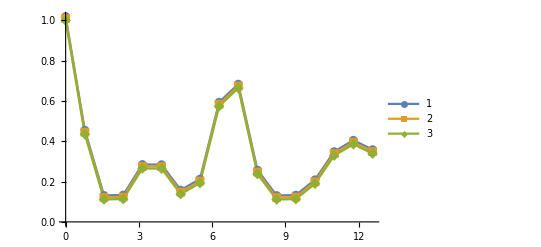

```mathematica
ListPlot[ {
 {rotationAngles, fchans+2*10^-2}ᵀ  
, {rotationAngles, fprocs + 1*10^-2}ᵀ
, {rotationAngles,  funi}ᵀ
}
,GridLines->{{}, {1/(systemdim+1)}}
, PlotLegends->Automatic
]
```

#### test with different interactions to bath:

```mathematica
nqubits = 2; 
bathdim  = 2; (* hardcoded *)
systemdim = 2^nqubits;

(* Create a funky parameterized unitary that implements sort of a SWAP operation *)

hamSystem = Sum[ qop[ splus, j, nqubits] . qop[ smin, 1, nqubits], {j,1,nqubits} ];
hamSystem = N[ hamSystem + hamSystem† ];

hamSB =    Sum[ qop[ splus, j, nqubits+1 ] . qop[ smin, nqubits+1, nqubits+1 ], {j,1,nqubits} ];
hamSB = N[ hamSB + hamSB†];

rotAngle = 5;
bathCouplings = Range[ 0, 4, 1/10];

fchans = {};
fprocs = {};
funi = {};

Do[ 

ham = kr[ hamSystem , Id2 ]  + cpl * hamSB;
uu = Chop[  MatrixExp[ -I N@ham *rotAngle ]  ]; 
goalU = Chop[ MatrixExp[ -I N @hamSystem * rotAngle ] ];

(* Create a quantum process: *)
process[ rho_ ] := partialTrace[ uu.addQubit[rho].uu† , {systemdim,bathdim}, {1} ];

(* Turn into Liouville-form channel *)
channel = LiouvilleRepresentation[ process, systemdim ] ;

(* Store different fidelities *)
fchans = Append[ fchans, GateFidelityFromChannel[ channel ]  ];
fprocs = Append[ fprocs, GateFidelityFromProcess[ process, systemdim ]  ];
funi = Append[ funi, GateFidelityProcessVsUnitary[ process, goalU ] ];

,{ cpl, bathCouplings }];
```

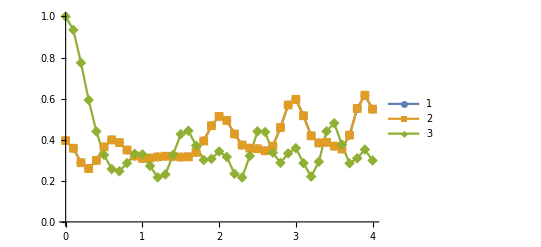

```mathematica
ListPlot[ {
 {bathCouplings, fchans}ᵀ  
, {bathCouplings, fprocs}ᵀ
, {bathCouplings,  funi}ᵀ
}
,GridLines->{{}, {1/(systemdim+1)}}
, PlotLegends->Automatic
]
```